The idea is to make a two point vector Pade approximation.  
	f⃗(x)≈(p⃗(x))/(q(x))
In practice the dimension is large.  I am going to experiment to see if I can use an averaged scalar data set to construct 
	q(x)=1+q_1 x+…+q_n x^n
and then subsequently compute each component of p⃗(x) as just the two point “Hermite” fit to f⃗(x)q(x)≈p(x).

Each component "i" would generate a different denominator.   The hope is to use some averaged data to produce a single “uniform” denominator.

## Scalar Pade Approximation

The scalar problem to approximate  f(x)≈p(x)/q(x) with p(x) of degree m and q(x) of degree n with q(0)=1 is standard. All I do is clear the fraction and match coefficients.  It looks like this
	q(x)f(x)-p(x)=0+0 x+…+0 x^m+0 x^(m+1)+…+0 x^(m+n)+O(x^(n+m+1))
The m+1 coefficients in the numerator p(x) are directly determined by the first  m+1 equations.  The n unknown coefficients in the denominator q(x) are determined by the next n equations.  The coefficients of q(x)*f(x) are the convolution of the coefficients of q(x) and a sufficiently long truncation of the power series for f.  Some parts of the literature tends to use any element of the null space of the n×(m+1) Toeplitz matrix
	T=(f[m+1] | f[m] | … | f[1]
f[m+2] | f[m+1] |   | f[2]
⋮ |   |   |  
f[m+n] |   |   |  )
as the coefficients of the denominator.  I am making the decision that I am using raw polynomials. I will add i! scalings to and from the power series representations if (and when) needed.  I am hedging on the decision to use the solution q(x)=1+q_1 x+… 	For now I am going to hold onto q_0 in the derivation.

```mathematica
Clear[m,n,f,fs,p,ps,q,qs]
{m,n}={7,3};
{fs,ps,qs}={
Array[f,m+n+1,0],
Array[p,m+1,0],
Array[q,n+1,0]};
CoeffToPoly[coeffs_List,x_]:=Sum[coeffs⟦i⟧x^(i-1),{i,Length[coeffs]}]
Eqs=CoefficientList[CoeffToPoly[fs,x]CoeffToPoly[qs,x]-CoeffToPoly[ps,x],x]⟦1;;m+n+1⟧;
TableForm[Eqs⟦1;;m+1⟧,TableHeadings->{Table[x^i,{i,0,m}],Automatic}]
TableForm[Eqs⟦m+2;;m+n+1⟧,TableHeadings->{Table[x^i,{i,m+1,m+n}],Automatic}]
```

1 | -p[0]+f[0] q[0]
x | -p[1]+f[1] q[0]+f[0] q[1]
x^2 | -p[2]+f[2] q[0]+f[1] q[1]+f[0] q[2]
x^3 | -p[3]+f[3] q[0]+f[2] q[1]+f[1] q[2]+f[0] q[3]
x^4 | -p[4]+f[4] q[0]+f[3] q[1]+f[2] q[2]+f[1] q[3]
x^5 | -p[5]+f[5] q[0]+f[4] q[1]+f[3] q[2]+f[2] q[3]
x^6 | -p[6]+f[6] q[0]+f[5] q[1]+f[4] q[2]+f[3] q[3]
x^7 | -p[7]+f[7] q[0]+f[6] q[1]+f[5] q[2]+f[4] q[3]

x^8 | f[8] q[0]+f[7] q[1]+f[6] q[2]+f[5] q[3]
x^9 | f[9] q[0]+f[8] q[1]+f[7] q[2]+f[6] q[3]
x^10 | f[10] q[0]+f[9] q[1]+f[8] q[2]+f[7] q[3]

```mathematica
MatrixForm[
CoefficientArrays[
Eqs⟦m+2;;m+n+1⟧,
qs]⟦2⟧]
```

(f[8] | f[7] | f[6] | f[5]
f[9] | f[8] | f[7] | f[6]
f[10] | f[9] | f[8] | f[7])

The terms x^(m+1) up to x^(m+n) are determined by the Toeplitz matrix

```mathematica
Clear[f]
T=ToeplitzMatrix[Table[f[i],{i,m+1,m+n,1}],Table[f[i],{i, m+1,1+m-n,-1}]];
T=T/.f[i_]:>If[i≥0,f[i],0];
MatrixForm[T]
```

(f[8] | f[7] | f[6] | f[5]
f[9] | f[8] | f[7] | f[6]
f[10] | f[9] | f[8] | f[7])

OK.  I should be able to test this against the built in Pade Approximants.  For a

The process breaks for some functions and orders.

```mathematica
Clear[f,fun,x]
fun[x_]:=Cos[x]
pMax=21;
Table[
f[i]=Coefficient[Normal[Series[fun[x],{x,0,pMax+1}]],x,i],
{i,0,pMax,1}];
{m,n}={7,7};
pad[x_]=PadeApproximant[fun[x],{x,0, {m,n}}];
T=ToeplitzMatrix[Table[f[i],{i,m+1,m+n,1}],Table[f[i],{i, m+1,1+m-n,-1}]];
T=T/.f[i_]:>If[i≥0,f[i],0];
MatrixForm[T];
{v1}=NullSpace[T]
v1=v1/v1⟦1⟧
CoefficientList[Denominator[pad[x]],x]
```

{{0,39251520/127,0,1154160/127,0,16632/127,0,1}}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{Indeterminate,ComplexInfinity,Indeterminate,ComplexInfinity,Indeterminate,ComplexInfinity,Indeterminate,ComplexInfinity}

{1,0,229/7788,0,1/2360,0,127/39251520}

```mathematica
{m,n}
pad[x]
```

{7,7}

(1-(3665 x^2)/7788+(711 x^4)/25960-(2923 x^6)/7850304)/(1+(229 x^2)/7788+x^4/2360+(127 x^6)/39251520)

0.841471/(1.-0.89893 x+1.73671 x^2-1.99715 x^3+2.95729 x^4-3.79095 x^5+5.24135 x^6)

1.1884-1.06828 x+2.06389 x^2-2.37341 x^3+3.51443 x^4-4.50514 x^5+6.2288 x^6

1.1884-1.06828 x+2.06389 x^2-2.37341 x^3+3.51443 x^4-4.50514 x^5+6.2288 x^6

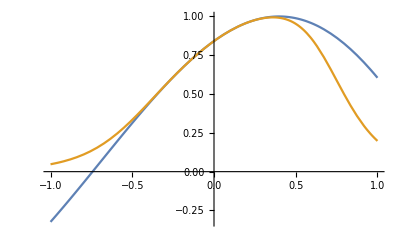

```mathematica
f[x_]:=Sin[Exp[0.4 x]+x]
p[x_]=N[PadeApproximant[f[x],{x,0,{0,6}}]]
Simplify[1/p[x]]
Expand[N[Normal[Series[1/f[x],{x,0, 6}]]]]
Plot[{f[x],p[x]},{x, -1,1}]
```

```mathematica
Clear[f,fun,x]
fun[x_]:=Exp[x]/((1-x)^2+1/1000)
pMax=21;
Table[
f[i]=Coefficient[Normal[Series[fun[x],{x,0,pMax+1}]],x,i],
{i,0,pMax,1}];
{m,n}={5,5};
pad[x_]=PadeApproximant[fun[x],{x,0, {m,n}}];
T=ToeplitzMatrix[Table[f[i],{i,m+1,m+n,1}],Table[f[i],{i, m+1,1+m-n,-1}]];
T=T/.f[i_]:>If[i≥0,f[i],0];
MatrixForm[T];
{v1}=NullSpace[T];
v1=v1/v1⟦1⟧
CoefficientList[Denominator[pad[x]],x]
```

{1,-232408464109788754660721143/97619723002948778075730286,799493989077988243167863143/439288753513269501340786287,-1750066436406072854559291143/3514310028106156010726290296,3084125806094042588835005143/49200340393486184150168064144,-4801672098141897445995005143/1476010211804585524505041924320}

{1,-232408464109788754660721143/97619723002948778075730286,799493989077988243167863143/439288753513269501340786287,-1750066436406072854559291143/3514310028106156010726290296,3084125806094042588835005143/49200340393486184150168064144,-4801672098141897445995005143/1476010211804585524505041924320}

```mathematica
NullSpace[T]
```

{{-3165565566240/9376239571,1186285428720/9376239571,-3334807267680/9376239571,1195661794740/9376239571,-169241787990/9376239571,1}}

```mathematica
fun[x]
pad[x]
```

ⅇ^x/(1/1000+(1-x)^2)

(1000/1001+(30097732516210432719071500 x)/48809861501474389037865143+(76133425597104440868143000 x^2)/439288753513269501340786287+(86843993571545518760625125 x^3)/3075021274592886509385504009+(16811489763960091608767875 x^4)/6150042549185773018771008018+(4793586529498564036053575 x^5)/36900255295114638112626048108)/(1-(232408464109788754660721143 x)/97619723002948778075730286+(799493989077988243167863143 x^2)/439288753513269501340786287-(1750066436406072854559291143 x^3)/3514310028106156010726290296+(3084125806094042588835005143 x^4)/49200340393486184150168064144-(4801672098141897445995005143 x^5)/1476010211804585524505041924320)

```mathematica
den[x_]=Denominator[pad[x]]
```

1-(232408464109788754660721143 x)/97619723002948778075730286+(799493989077988243167863143 x^2)/439288753513269501340786287-(1750066436406072854559291143 x^3)/3514310028106156010726290296+(3084125806094042588835005143 x^4)/49200340393486184150168064144-(4801672098141897445995005143 x^5)/1476010211804585524505041924320

```mathematica
den[0.1]
```

0.779633

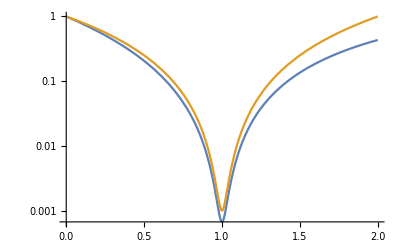

```mathematica
LogPlot[{den[x],1/1000+(1-x)^2},{x,0, 2}]
```

```mathematica
Solve[Denominator[pad[x]]==0,x]//N
```

{{x→6.40205},{x→1.-0.0316222 ⅈ},{x→1.+0.0316222 ⅈ},{x→5.43351-4.29465 ⅈ},{x→5.43351+4.29465 ⅈ}}

{5,5}

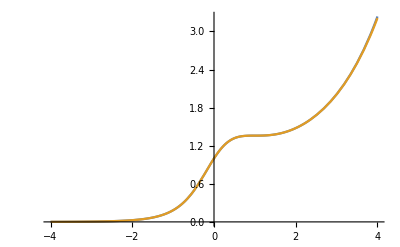

```mathematica
{m,n}
Plot[{pad[x],fun[x]},{x,-4,4}]
```

```mathematica
Dimensions[T]
SingularValueList[N[T]]
NullSpace[T]
```

{7,8}

{0.503462,0.503462,0.00207295,0.00207295,3.86712×10^-7,3.86545×10^-7,1.33825×10^-11}

{{0,39251520/127,0,1154160/127,0,16632/127,0,1}}

```mathematica
PadeApproximant[fun[x],{x,0, {m,n}}]
```

(1-(3665 x^2)/7788+(711 x^4)/25960-(2923 x^6)/7850304)/(1+(229 x^2)/7788+x^4/2360+(127 x^6)/39251520)